## Exercise 21—Laplace Transform

## Exercise 1

Let f(t)=3. Calculate the Laplace transform of this function.

### Solution

To calculate the Laplace transform of f(t)=3, it is necessary to evaluate the improper integral:

L{3}=F(s)=∫_0^∞ 3 e^(-s t)ⅆt

This improper integral can be calculated with Integrate:

```mathematica
Integrate[3 Exp[-s t],{t,0,∞}]
```

The result shows that the Laplace transform of the function f(t)=3 is the function F(s)=3/s.

Verify this result with LaplaceTransform:

```mathematica
LaplaceTransform[3,t,s]
```

## Exercise 2

Let f(t)=e^(2 t). Calculate the Laplace transform of this function.

### Solution

To calculate the Laplace transform of f(t)=e^(2 t), it is necessary to evaluate the improper integral:

L{e^(2 t)}=F(s)=∫_0^∞ e^(2 t)e^(-s t)ⅆt

This improper integral can be calculated with Integrate:

```mathematica
Integrate[Exp[2 t]Exp[-s t],{t,0,∞}]
```

The result shows that the Laplace transform of the function f(t)=e^(2 t) is the function F(s)=1/(s-2).

Verify this result with LaplaceTransform:

```mathematica
LaplaceTransform[Exp[2 t],t,s]
```

## Exercise 3

Let f(t)=t for 0<=t<1 and 0 elsewhere. Calculate the Laplace transform of this function.

### Solution

To calculate the Laplace transform of this function, it is necessary to evaluate the improper integral:

L{f(t)}=F(s)=∫_0^∞ f(t)e^(-s t)ⅆt

The function f(t) can be defined with Piecewise:

```mathematica
f[t_]:=Piecewise[{{t,0≤t<1},{0,t<0},{0,t≥1}}]
```

The improper integral can now be evaluated:

```mathematica
Integrate[f[t]Exp[-s t] ,{t,0,Infinity}]
```

Verify this result with LaplaceTransform:

```mathematica
LaplaceTransform[f[t],t,s]
```

## Exercise 4

The Laplace transform of a function of two variables can be computed using the following formula:

L{f(x,y)}=F(s_1,s_2)=∫_0^∞ ∫_0^∞ f(x,y)e^(-(s_1 x+s_2 y))ⅆxⅆy

Use this formula to calculate the Laplace transform of the function:

f(x,y)=1

### Solution

To calculate the Laplace transform of f(x,y)=1, it is necessary to evaluate the improper integral:

L{1}=F(s_1,s_2)=∫_0^∞ ∫_0^∞ 1 e^(-(s_1 x+s_2 y))ⅆxⅆy

This improper integral can be calculated with Integrate:

```mathematica
Integrate[1Exp[-(Subscript[s, 1] x+Subscript[s, 2] y)],{x,0,∞},{y,0,∞}]//Quiet
```

Verify this result with LaplaceTransform:

```mathematica
LaplaceTransform[1,{x,y},{Subscript[s, 1],Subscript[s, 2]}]
```

## Exercise 5

The Laplace transform of a function of two variables can be computed using the following formula:

L{f(t_1,t_2)}=F(s_1,s_2)=∫_0^∞ ∫_0^∞ f(t_1,t_2)e^(-(s_1 t_1+s_2 t_2))ⅆ t_1ⅆ t_2

Use this formula to calculate the Laplace transform of the function:

f(x,y)=1/(√(x+y))

### Solution

To calculate the Laplace transform of f(x,y)=e^(a x+b y), it is necessary to evaluate the improper integral:

L{1/(√(x+y))}=F(s_1,s_2)=∫_0^∞ ∫_0^∞ 1/(√(x+y))e^(-(s_1 x+s_2 y))ⅆxⅆy

This improper integral can be calculated with Integrate:

```mathematica
Integrate[1/(√(x+y))Exp[-(Subscript[s, 1] x+Subscript[s, 2] y)],{x,0,∞},{y,0,∞}]
```

Verify this result with LaplaceTransform:

```mathematica
LaplaceTransform[1/(√(x+y)),{x,y},{Subscript[s, 1],Subscript[s, 2]}]
```

## Exercise 22—Transforming Initial Value Problems

## Exercise 1

Use the Laplace transform to solve the following initial value problem:

y''(t)-y(t)=0

y(0)=1

y'(0)=1

### Solution

First, apply the Laplace transform to the differential equation:

```mathematica
lt=LaplaceTransform[y''[t]-y[t]==0,t,s]
```

Substitute y(0)=1 and y'(0)=1 using the initial conditions:

```mathematica
lt2=lt/.{y[0]->1,y'[0]->1}
```

Next, solve for L{y(t)}, the Laplace transform of the unknown function:

```mathematica
Solve[lt2,LaplaceTransform[y[t],t,s]]
```

Calculate the inverse Laplace transform to obtain the solution to the initial value problem:

```mathematica
InverseLaplaceTransform[1/(-1+s),s,t]
```

Verify the result with DSolveValue:

```mathematica
DSolveValue[{y''[t]-y[t]==0,y[0]==1,y'[0]==1},y[t],t]
```

## Exercise 2

Use the Laplace transform to solve the following initial value problem:

y''(t)-y(t)=sin(t)

y(0)=0

y'(0)=1

### Solution

First, apply the Laplace transform to the differential equation:

```mathematica
lt=LaplaceTransform[y''[t]-y[t]==Sin[t],t,s]
```

Substitute y(0)=0 and y'(0)=1 using the initial conditions:

```mathematica
lt2=lt/.{y[0]->0,y'[0]->1}
```

Next, solve for L{y(t)}, the Laplace transform of the unknown function:

```mathematica
Solve[lt2,LaplaceTransform[y[t],t,s]]
```

Calculate the inverse Laplace transform to obtain the solution to the initial value problem:

```mathematica
InverseLaplaceTransform[(2+s^2)/((-1+s^2) (1+s^2)),s,t]//Simplify
```

Verify the result with DSolveValue:

```mathematica
DSolveValue[{y''[t]-y[t]==Sin[t],y[0]==0,y'[0]==1},y[t],t]//Simplify
```

## Exercise 3

Use the Laplace transform to solve the following initial value problem:

y^(5)(t)-3y^(4)(t)+3y^(3)(t)-y^(2)(t)=0

y(0)=1

y^(1)(0)=1

y^(2)(0)=0

y^(3)(0)=0

y^(4)(0)=0

### Solution

First, apply the Laplace transform to the differential equation:

```mathematica
lt=LaplaceTransform[D[y[t],{t,5}]-3D[y[t],{t,4}]+3D[y[t],{t,3}]-D[y[t],{t,2}]==0,t,s]
```

Substitute in the the initial conditions:

```mathematica
lt2=lt/.{y[0]->1,y'[0]->1,y''[0]->0,y'''[0]->0,y''''[0]->0}
```

Solve for L{y(t)}, the Laplace transform of the unknown function:

```mathematica
Solve[lt2,LaplaceTransform[y[t],t,s]]
```

Calculate the inverse Laplace transform to obtain the solution to the initial value problem:

```mathematica
InverseLaplaceTransform[(1+s)/s^2,s,t]
```

Verify the result with DSolveValue:

```mathematica
DSolveValue[{D[y[t],{t,5}]-3D[y[t],{t,4}]+3D[y[t],{t,3}]-D[y[t],{t,2}]==0,y[0]==1,y'[0]==1,y''[0]==0,y'''[0]==0,y''''[0]==0},y[t],t]
```

## Exercise 4

Use the Laplace transform to solve the following initial value problem:

y'''(t)-y'(t)=sin(t)

y(0)=a

y'(0)=b

y''(0)=c

Where a, b and c are constants.

### Solution

First, apply the Laplace transform to the differential equation:

```mathematica
lt=LaplaceTransform[y'''[t]-y'[t]==Sin[t],t,s]
```

Substitute y(0)=a, y'(0)=b, and y''(0)=c from the initial conditions:

```mathematica
lt2=lt/.{y[0]->a,y'[0]->b,y''[0]->c}
```

Solve for L{y(t)}, the Laplace transform of the unknown function:

```mathematica
Solve[lt2,LaplaceTransform[y[t],t,s]]
```

Calculate the inverse Laplace transform to obtain the solution to the initial value problem:

```mathematica
InverseLaplaceTransform[(1-a+c+b s+c s^2+b s^3+a s^4)/((1+s^2) (-s+s^3)),s,t]//Expand
```

Verify the result with DSolveValue:

```mathematica
DSolveValue[{y'''[t]-y'[t]==Sin[t],y[0]==a,y'[0]==b,y''[0]==c},y[t],t]//Expand
```

## Exercise 5

Use the Laplace transform to solve the following initial value problem:

a y''(t)+b y'(t)+c y(t)=0

y(0)=0

y'(0)=1

Where a, b and c are constants.

### Solution

First, apply the Laplace transform to the differential equation:

```mathematica
lt=LaplaceTransform[a y''[t]+b y'[t]+c y[t]==0,t,s]
```

Substitute y(0)=0 and y'(0)=1 using the initial conditions:

```mathematica
lt2=lt/.{y[0]->0,y'[0]->1}
```

Solve for L{y(t)}, the Laplace transform of the unknown function:

```mathematica
Solve[lt2,LaplaceTransform[y[t],t,s]]
```

Calculate the inverse Laplace transform to obtain the solution to the initial value problem:

```mathematica
InverseLaplaceTransform[a/(c+b s+a s^2),s,t]
```

Verify the result with DSolveValue:

```mathematica
DSolveValue[{a y''[t]+b y'[t]+c y[t]==0,y[0]==0,y'[0]==1},y[t],t]
```

## Exercise 23—Step Functions

## Exercise 1

Construct the following function using unit step functions:

f(t)=Piecewise[{{0
-2
 2, t<2
2<=t<4
4<=t<6}, {1, t>=6}}]

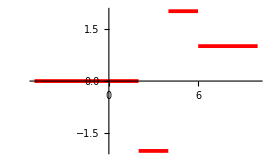

### Solution

The unit step function θ(t) appears as follows:

```mathematica
Plot[UnitStep[t],{t,-5,5},]
```

Start with the first nonzero value defined and build in order.

The first nonzero value is -2 when the function is between t=2 and t=4.

This can be constructed by shifting the UnitStep function two units to the right, and multiplying it by -2:

```mathematica
Plot[-2UnitStep[t-2],{t,-5,10},]
```

The next nonzero value is when the function equals 2 for 4<=t<6.

Since the -2θ(t-2) term already equals -2 in this region, it is necessary to add 4 so that the total sum is 2.

This is accomplished by including a UnitStep function shifted 4 units to the right and multiplied by 4:

```mathematica
Plot[-2UnitStep[t-2]+4UnitStep[t-4],{t,-5,10},]
```

The last nonzero value occurs when the function equals 1 for t>=6.

To get this last term, use a UnitStep function shifted 6 units to the right and multiplied by -1 so that the sum of this term and all previous terms equals 1 when t>6:

```mathematica
Plot[-2UnitStep[t-2]+4UnitStep[t-4]-1UnitStep[t-6],{t,-5,10},]
```

This result can be confirmed by constructing a Piecewise function and testing its equality through PiecewiseExpand:

```mathematica
-2UnitStep[t-2]+4UnitStep[t-4]-1UnitStep[t-6]==PiecewiseExpand[Piecewise[{{0,t<2},{-2,2≤t<4},{2,4≤ t<6},{1,t≥ 6}}]]//FullSimplify
```

## Exercise 2

Construct the following function using unit step functions:

f(t)=Piecewise[{{t^3
1
0, 0<=t<1
t>=1
otherwise}}]

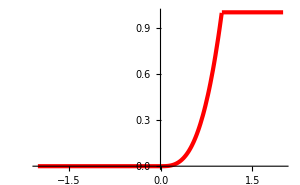

### Solution

The unit step function θ(t) appears as follows:

```mathematica
Plot[UnitStep[t],{t,-5,5},]
```

Start with the first value defined and build in order.

The first nonzero value is t^3 when the function is between t=0 and t=1.

This can be constructed by multiplying t^3 with the UnitStep function:

```mathematica
Plot[t^3 UnitStep[t],{t,-2,2},]
```

The function f(t) is equal to 1 when t>=1, so it is necessary to subtract the t^3 term when t>=1, then add the constant 1 in this region.

First, subtract the t^3 term for t>=1:

```mathematica
Plot[t^3 UnitStep[t] -t^3 UnitStep[t-1],{t,-2,2},]
```

Now, add the constant 1 when t>1 using 1*θ(t-1):

```mathematica
Plot[t^3 UnitStep[t] -t^3 UnitStep[t-1]+UnitStep[t-1],{t,-2,2},]
```

This result can be confirmed by constructing a Piecewise function and testing its equality through PiecewiseExpand:

```mathematica
t^3 UnitStep[t] -t^3 UnitStep[t-1]+UnitStep[t-1]==PiecewiseExpand[Piecewise[{{0,t<0},{t^3,0≤t<1},{1,1≤ t}}]]//FullSimplify
```

## Exercise 3

Using the properties of the UnitStep function, calculate the Laplace transform of this piecewise function:

f(t)=Piecewise[{{0, t<3}, {t-3, t>=3}}]

### Solution

Notice that f(t) can be written using the UnitStep function as:

f(t)=θ(t-3) *(t-3)

In the lesson it was learned that:

L{θ(t-c)f(t-c)}=e^(-c s)L{f(t)}

Therefore, with c=3, the Laplace transform of f(t) can be calculated:

```mathematica
Exp[-3 s] LaplaceTransform[t, t,s]
```

This can be confirmed by first defining f(t) as a piecewise function in the Wolfram Language:

```mathematica
f[t_]:=Piecewise[{{0,0≤t<3},{(t-3),t≥3}}]
```

Applying LaplaceTransform to the function f(t) directly confirms the result using the UnitStep function:

```mathematica
LaplaceTransform[f[t],t,s]
```

## Exercise 4

Using the properties of the UnitStep function, calculate the Laplace transform of this piecewise function:

f(t)=Piecewise[{{0, t<1}, {t-1
0, 1<=t<2
t>=2}}]

### Solution

Rewrite f(t)=g(t)+r(t) where g(t) is defined as:

g(t)=Piecewise[{{0, t<1}, {(t-1)θ[t-1], t>=1}}]

and r(t) is defined as:

r(t)=Piecewise[{{0, t<2}, {-(t-1)θ[t-2], t>=2}}]

with θ(t) being the UnitStep function.

With these definitions:

L{f(t)}=L{g(t)+r(t)}=L{g(t)}+L{r(t)}

Since:

L{θ(t-c)h(t-c)}=e^(-c s)L{h(t)}

the Laplace transform of f(t) can be calculated as:

L{f(t)}=L{g(t)}+L{r(t)}=e^(-1 s)L{t}+L{r(t)}

Note that the second term in r(t) can be written as -((t-2)+1)θ(t-2), so that L{r(t)} becomes:

L{r(t)}=e^(-2 s)L{-(t+1)}

L{r(t)} can now be calculated explicitly:

```mathematica
Exp[-1 s]LaplaceTransform[t,t,s]+Exp[-2 s]LaplaceTransform[-(t+1),t,s]//Expand
```

This can be confirmed by first defining f(t) as a piecewise function in the Wolfram Language:

```mathematica
f[t_]:=Piecewise[{{0,t<1},{(t-1),2>t≥1},{0,t≥2}}]
```

Applying LaplaceTransform to the function f(t) directly confirms the result using the UnitStep function.

```mathematica
LaplaceTransform[f[t],t,s]//Expand
```

## Exercise 5

Using the properties of the UnitStep function, calculate the Laplace transform of this piecewise function:

f(t)=Piecewise[{{0, t<1}, {e^(-(t-1)), t>=1}}]

### Solution

Notice that f(t) can be written using the UnitStep function as:

f(t)=θ(t-1)e^(-(t-1))

In the lesson it was learned that:

L{θ(t-c)f(t-c)}=e^(-c s)L{f(t)}

Therefore, with c=1, the Laplace transform of f(t) can be calculated:

```mathematica
Exp[-1 s]LaplaceTransform[Exp[-t],t,s]
```

Thus the final answer must be the following:

```mathematica
E^(-1*s)*LaplaceTransform[Exp[-t], t,s]
```

This can be confirmed by first defining f(t) as a piecewise function in the Wolfram Language:

```mathematica
f[t_]:=Piecewise[{{0,t<1},{E^(-(t-1)),t≥1}}]
```

Applying LaplaceTransform to the function f(t) directly confirms the result using the UnitStep function:

```mathematica
LaplaceTransform[f[t],t,s]
```